```mathematica
(*Part 1A*)
```

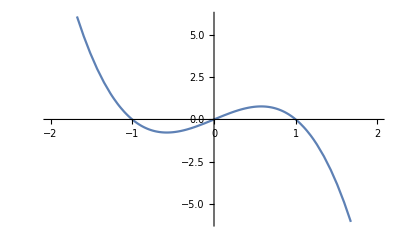

```mathematica
Plot[2y-2y^3,{y,-2,2}]
```

```mathematica
(*Steady States at y=-1, y=0, y=1
y=-1 is stable
y=0 is unstable
y=1 is stable*)
```

```mathematica
Integrate[1/(2y-2y^3),y]
```

Log[y]/2-1/4 Log[1-y^2]

```mathematica
(*Initial Value 1 is y(0) = 1.5
Initial Value 2 is y(0) = 0.5*)
```

```mathematica
vv1 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==1.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

```mathematica
vv2 = NDSolveValue[{y'[t]==2y[t]-2y[t]^3,y[0]==.5},y,{t,0,20}]
```

InterpolatingFunction[{{0., 20.}}, <>]

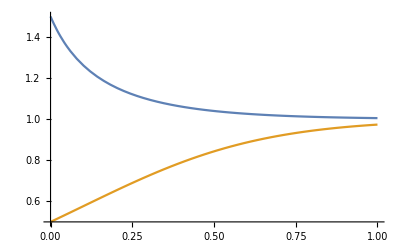

```mathematica
Plot[{vv1[t],vv2[t]},{t,0,1}]
```

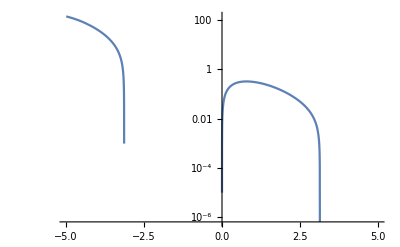

```mathematica
(*Part 1B*)
LogPlot[Exp[-y]*Sin[y],{y,-5,5},PlotRange->Full]
```

```mathematica
(*Steady States at y=n*Pi for any integer n*)
Integrate[Exp[x]*Sec[x],x]
```

(1-ⅈ) ⅇ^((1+ⅈ) x) Hypergeometric2F1[1/2-ⅈ/2,1,3/2-ⅈ/2,-ⅇ^(2 ⅈ x)]

```mathematica
(*Problem 2*)
Manipulate[Plot[kk*y*(y-1)*(y-2)*(y-3),{y,-1,5}],{kk,0,20}]
```

```mathematica
(*The above equation satisies it
and that will hold as long as k>0
INSERT SECOND DERIVATIVE EXPLANATION*)
```